```mathematica
BucketCompare[b1_,b2_]:=Min[b1]<Min[b2]
```

```mathematica
TwoElements[n_]:=Block[{all=Range[n],result={}},
Table[
AppendTo[result,Sort[Join[{s},Map[{#}&,Select[all,!MemberQ[s,#]&]]],BucketCompare]]
,{s,Subsets[all,{2}]}
];
result
]
```

```mathematica
BlockPrint[block_]:=StringJoin[Map[ToString[#]&,block]]
```

```mathematica
PartitionPrint[sets_]:=StringRiffle[Map[BlockPrint[#]&,sets],"|"]
```

```mathematica
Map[PartitionPrint,TwoElements[5]]
```

{12|3|4|5,13|2|4|5,14|2|3|5,15|2|3|4,1|23|4|5,1|24|3|5,1|25|3|4,1|2|34|5,1|2|35|4,1|2|3|45}

```mathematica
Joins[sets_]:=Block[{result={}},
Table[
AppendTo[result,Sort[Join[{Sort[Flatten[s]]},Sort[Select[sets,!MemberQ[s,#]&]]],BucketCompare]]
,{s,Subsets[sets,{2}]}
];
Sort[Map[Sort[#,BucketCompare]&,result]]
]
```

```mathematica
PartitionPrint[{{1,2},{3},{4},{5}}]
```

12|3|4|5

```mathematica
Descendents[g_,vertices_]:=Descendents[g,vertices]=Block[{result={},nodes,edges,current},
nodes=vertices;
While[nodes≠{},
current=First[nodes];
nodes=Rest[nodes];
edges=Select[EdgeList[g],#[[1]]==current&];
result=Join[result,edges];
nodes=DeleteDuplicates[Join[nodes,Map[#[[2]]&,edges]]];
];
DeleteDuplicates[result]
]
```

```mathematica
Recurse[sets_]:=Recurse[sets]=Block[{result={}, joins, sub},
If[Length[sets]==1,
result={},

joins=Joins[sets];
result=Table[
sets->j,{j,joins}
];
Table[
sub=Recurse[j];
result=Join[result,sub],{j,joins}
]
];
result
]
```

```mathematica
;
```

```mathematica
PartitionIntersect[g_,vertices_]:=Block[{edges=DeleteDuplicates[Flatten[Table[Descendents[g,{v}],{v,vertices}],1]], vertic,counts},
vertic=DeleteDuplicates[Flatten[Table[{e[[1]],e[[2]]},{e,edges}],1]];
counts=Table[Length[v],{v,vertic}];
Map[Last,Sort[Tally[counts],#1>#2&]]
]
```

```mathematica
DoubleVertices=TwoElements[7]
```

{{{1,2},{3},{4},{5},{6},{7}},{{1,3},{2},{4},{5},{6},{7}},{{1,4},{2},{3},{5},{6},{7}},{{1,5},{2},{3},{4},{6},{7}},{{1,6},{2},{3},{4},{5},{7}},{{1,7},{2},{3},{4},{5},{6}},{{1},{2,3},{4},{5},{6},{7}},{{1},{2,4},{3},{5},{6},{7}},{{1},{2,5},{3},{4},{6},{7}},{{1},{2,6},{3},{4},{5},{7}},{{1},{2,7},{3},{4},{5},{6}},{{1},{2},{3,4},{5},{6},{7}},{{1},{2},{3,5},{4},{6},{7}},{{1},{2},{3,6},{4},{5},{7}},{{1},{2},{3,7},{4},{5},{6}},{{1},{2},{3},{4,5},{6},{7}},{{1},{2},{3},{4,6},{5},{7}},{{1},{2},{3},{4,7},{5},{6}},{{1},{2},{3},{4},{5,6},{7}},{{1},{2},{3},{4},{5,7},{6}},{{1},{2},{3},{4},{5},{6,7}}}

```mathematica
TableForm[
Sort[
Tally[
Monitor[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{1,2}]}
],
Map[PartitionPrint,set]]
]
],TableDepth->1
]
```

{{1,15,65,90,31,1},21}
{{2,29,120,155,47,1},210}

```mathematica
MemoryInUse[]
```

2076165000

```mathematica
TableForm[
Sort[
Tally[
Monitor[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{1,Length[DoubleVertices]}]}
],
Map[PartitionPrint,set]]
]
],TableDepth->1
]
```

{{1,15,65,90,31,1},21}
{{2,29,120,155,47,1},210}
{{3,42,166,201,55,1},1295}
{{3,43,175,220,63,1},35}
{{4,54,203,228,55,1},105}
{{4,54,204,233,59,1},5250}
{{4,55,212,247,63,1},630}
{{5,65,234,251,59,1},1575}
{{5,65,235,255,61,1},13377}
{{5,65,235,256,63,1},252}
{{5,66,242,265,63,1},4935}
{{5,67,249,274,63,1},210}
{{6,75,257,260,59,1},210}
{{6,75,259,267,61,1},9135}
{{6,75,260,270,61,1},420}
{{6,75,260,270,62,1},16807}
{{6,75,260,271,63,1},2772}
{{6,76,265,274,63,1},1260}
{{6,76,266,277,63,1},20090}
{{6,77,272,283,63,1},3535}
{{6,79,286,301,63,1},35}
{{7,84,277,273,61,1},2310}
{{7,84,278,276,61,1},1260}
{{7,84,279,278,62,1},20580}
{{7,84,279,280,63,1},1260}
{{7,84,280,280,62,1},2520}
{{7,84,280,280,63,1},360}
{{7,84,280,281,63,1},8820}
{{7,85,284,283,63,1},15225}
{{7,85,285,285,63,1},36015}
{{7,85,285,286,63,1},2520}
{{7,86,288,283,63,1},630}
{{7,86,290,289,63,1},22785}
{{7,87,295,292,63,1},1470}
{{7,88,302,301,63,1},525}
{{8,92,290,276,61,1},105}
{{8,92,291,279,61,1},630}
{{8,92,293,282,62,1},7350}
{{8,92,294,284,62,1},8190}
{{8,92,295,285,62,1},1260}
{{8,92,295,286,63,1},2520}
{{8,92,295,287,63,1},7560}
{{8,92,296,288,63,1},1260}
{{8,93,297,286,63,1},2520}
{{8,93,298,289,63,1},2520}
{{8,93,299,289,63,1},52920}
{{8,93,300,290,63,1},2520}
{{8,93,300,291,63,1},16380}
{{8,94,302,289,63,1},6930}
{{8,94,303,292,63,1},10080}
{{8,94,304,293,63,1},56595}
{{8,94,304,295,63,1},1260}
{{8,95,308,295,63,1},18900}
{{8,96,311,292,63,1},315}
{{8,96,314,301,63,1},3045}
{{8,97,318,301,63,1},630}
{{9,99,300,282,61,1},70}
{{9,99,303,284,62,1},630}
{{9,99,304,286,62,1},3780}
{{9,99,305,287,62,1},2520}
{{9,99,306,288,62,1},840}
{{9,99,306,289,63,1},1260}
{{9,99,306,290,63,1},420}
{{9,99,307,291,63,1},2520}
{{9,99,307,292,63,1},630}
{{9,100,309,291,63,1},16170}
{{9,100,310,292,63,1},11340}
{{9,100,310,293,63,1},15120}
{{9,100,311,293,63,1},5040}
{{9,100,311,294,63,1},8820}
{{9,100,312,295,63,1},840}
{{9,101,310,289,63,1},630}
{{9,101,311,292,63,1},2520}
{{9,101,312,295,63,1},420}
{{9,101,313,293,63,1},22050}
{{9,101,314,295,63,1},69300}
{{9,101,315,295,63,1},1260}
{{9,101,315,296,63,1},11340}
{{9,101,315,297,63,1},7560}
{{9,102,316,295,63,1},8820}
{{9,102,317,298,63,1},2520}
{{9,102,318,297,63,1},69825}
{{9,103,320,295,63,1},3465}
{{9,103,321,298,63,1},8505}
{{9,103,322,301,63,1},1260}
{{9,103,323,301,63,1},6860}
{{9,104,326,301,63,1},7385}
{{9,106,334,301,63,1},210}
{{10,105,310,285,62,1},21}
{{10,105,311,288,62,1},420}
{{10,105,312,288,62,1},630}
{{10,105,313,289,62,1},1260}
{{10,105,315,292,63,1},630}
{{10,106,316,292,63,1},840}
{{10,106,317,293,63,1},5040}
{{10,106,318,294,63,1},5040}
{{10,106,318,295,63,1},2520}
{{10,106,319,295,63,1},2520}
{{10,106,319,296,63,1},2520}
{{10,107,319,293,63,1},3780}
{{10,107,320,295,63,1},15120}
{{10,107,321,295,63,1},8820}
{{10,107,321,296,63,1},12600}
{{10,107,321,297,63,1},2520}
{{10,107,322,296,63,1},6300}
{{10,107,322,297,63,1},21420}
{{10,107,323,297,63,1},1260}
{{10,107,323,298,63,1},5040}
{{10,107,323,299,63,1},1260}
{{10,108,320,295,63,1},420}
{{10,108,324,297,63,1},56070}
{{10,108,325,298,63,1},42000}
{{10,108,325,299,63,1},15120}
{{10,108,326,298,63,1},2520}
{{10,108,326,299,63,1},10080}
{{10,109,324,295,63,1},1575}
{{10,109,325,298,63,1},2520}
{{10,109,327,297,63,1},11025}
{{10,109,328,299,63,1},60900}
{{10,109,329,301,63,1},7980}
{{10,109,330,301,63,1},1260}
{{10,110,329,298,63,1},5040}
{{10,110,330,301,63,1},3024}
{{10,110,332,301,63,1},24990}
{{10,111,334,301,63,1},6300}
{{10,112,338,301,63,1},2310}
{{10,115,350,301,63,1},21}
{{11,110,318,290,62,1},420}
{{11,111,322,294,63,1},630}
{{11,111,324,295,63,1},1260}
{{11,112,323,293,63,1},210}
{{11,112,325,295,63,1},3150}
{{11,112,325,296,63,1},1260}
{{11,112,326,296,63,1},5040}
{{11,112,326,297,63,1},1260}
{{11,112,327,297,63,1},2520}
{{11,112,327,298,63,1},2520}
{{11,112,328,298,63,1},1260}
{{11,113,327,297,63,1},2520}
{{11,113,328,297,63,1},5670}
{{11,113,329,297,63,1},3780}
{{11,113,329,298,63,1},22680}
{{11,113,330,298,63,1},10080}
{{11,113,330,299,63,1},13860}
{{11,113,330,300,63,1},1260}
{{11,113,331,299,63,1},3780}
{{11,113,331,300,63,1},5040}
{{11,114,330,297,63,1},9450}
{{11,114,331,299,63,1},15120}
{{11,114,332,298,63,1},5040}
{{11,114,332,299,63,1},48510}
{{11,114,333,299,63,1},3780}
{{11,114,333,300,63,1},22680}
{{11,114,333,301,63,1},1260}
{{11,114,334,300,63,1},2520}
{{11,114,334,301,63,1},3150}
{{11,115,334,299,63,1},31815}
{{11,115,335,300,63,1},27951}
{{11,115,335,301,63,1},18144}
{{11,115,336,301,63,1},13860}
{{11,115,337,301,63,1},2520}
{{11,116,333,298,63,1},1680}
{{11,116,334,301,63,1},630}
{{11,116,338,301,63,1},41790}
{{11,117,338,301,63,1},2940}
{{11,117,341,301,63,1},7350}
{{11,118,342,301,63,1},4095}
{{11,120,350,301,63,1},231}
{{12,114,322,291,62,1},35}
{{12,116,329,296,63,1},1260}
{{12,117,331,297,63,1},1260}
{{12,117,331,298,63,1},840}
{{12,117,333,298,63,1},2520}
{{12,117,333,299,63,1},1260}
{{12,118,332,297,63,1},945}
{{12,118,333,297,63,1},630}
{{12,118,334,298,63,1},5040}
{{12,118,334,299,63,1},10500}
{{12,118,335,299,63,1},7560}
{{12,118,335,300,63,1},5040}
{{12,118,336,299,63,1},1260}
{{12,118,336,300,63,1},7560}
{{12,118,337,301,63,1},840}
{{12,119,336,299,63,1},15750}
{{12,119,337,299,63,1},7560}
{{12,119,337,300,63,1},25200}
{{12,119,337,301,63,1},1260}
{{12,119,338,300,63,1},12600}
{{12,119,338,301,63,1},10080}
{{12,119,339,301,63,1},5880}
{{12,120,337,299,63,1},10080}
{{12,120,338,301,63,1},3780}
{{12,120,339,300,63,1},30240}
{{12,120,340,300,63,1},420}
{{12,120,340,301,63,1},34650}
{{12,120,341,301,63,1},7560}
{{12,120,342,301,63,1},630}
{{12,121,341,301,63,1},17640}
{{12,121,342,301,63,1},30240}
{{12,121,343,301,63,1},3780}
{{12,121,344,301,63,1},420}
{{12,122,337,298,63,1},105}
{{12,122,344,301,63,1},25690}
{{12,123,342,301,63,1},1260}
{{12,124,346,301,63,1},1400}
{{12,124,350,301,63,1},735}
{{12,125,350,301,63,1},420}
{{13,120,333,297,63,1},210}
{{13,121,335,299,63,1},105}
{{13,121,336,298,63,1},630}
{{13,122,338,299,63,1},3780}
{{13,122,338,300,63,1},2520}
{{13,122,339,300,63,1},2520}
{{13,123,338,299,63,1},2310}
{{13,123,339,299,63,1},3780}
{{13,123,340,300,63,1},11340}
{{13,123,340,301,63,1},2520}
{{13,123,341,300,63,1},5040}
{{13,123,341,301,63,1},6300}
{{13,123,342,301,63,1},5040}
{{13,124,341,300,63,1},18480}
{{13,124,341,301,63,1},210}
{{13,124,342,300,63,1},3780}
{{13,124,342,301,63,1},13230}
{{13,124,343,301,63,1},20160}
{{13,124,344,301,63,1},2520}
{{13,125,340,299,63,1},630}
{{13,125,344,301,63,1},34860}
{{13,125,345,301,63,1},12600}
{{13,125,346,301,63,1},2520}
{{13,126,344,301,63,1},7560}
{{13,126,346,301,63,1},28665}
{{13,127,347,301,63,1},8400}
{{13,127,350,301,63,1},420}
{{13,128,350,301,63,1},2625}
{{13,129,346,301,63,1},315}
{{13,130,350,301,63,1},420}
{{14,125,340,299,63,1},525}
{{14,126,342,300,63,1},2520}
{{14,126,342,301,63,1},630}
{{14,126,343,301,63,1},360}
{{14,127,341,299,63,1},315}
{{14,127,342,300,63,1},2625}
{{14,127,343,300,63,1},5670}
{{14,127,344,301,63,1},10080}
{{14,127,345,301,63,1},3780}
{{14,128,343,300,63,1},1260}
{{14,128,344,301,63,1},1470}
{{14,128,345,301,63,1},12600}
{{14,128,346,301,63,1},11340}
{{14,128,347,301,63,1},2520}
{{14,129,346,301,63,1},15120}
{{14,129,347,301,63,1},15540}
{{14,129,348,301,63,1},2520}
{{14,130,348,301,63,1},18690}
{{14,130,350,301,63,1},1260}
{{14,131,347,301,63,1},1890}
{{14,131,350,301,63,1},2940}
{{14,132,350,301,63,1},2520}
{{14,135,350,301,63,1},105}
{{15,129,344,300,63,1},490}
{{15,130,344,300,63,1},1260}
{{15,130,345,301,63,1},252}
{{15,130,346,301,63,1},4095}
{{15,130,347,301,63,1},140}
{{15,131,346,301,63,1},3990}
{{15,131,347,301,63,1},7560}
{{15,131,348,301,63,1},2940}
{{15,132,347,301,63,1},630}
{{15,132,348,301,63,1},11340}
{{15,132,349,301,63,1},2520}
{{15,132,350,301,63,1},630}
{{15,133,348,301,63,1},4095}
{{15,133,349,301,63,1},5915}
{{15,133,350,301,63,1},2100}
{{15,134,350,301,63,1},5670}
{{15,136,350,301,63,1},630}
{{15,140,350,301,63,1},7}
{{16,132,345,300,63,1},105}
{{16,133,347,301,63,1},1260}
{{16,133,348,301,63,1},1680}
{{16,134,348,301,63,1},2835}
{{16,134,349,301,63,1},2520}
{{16,134,350,301,63,1},420}
{{16,135,349,301,63,1},3780}
{{16,135,350,301,63,1},2772}
{{16,136,350,301,63,1},3465}
{{16,137,350,301,63,1},1470}
{{16,140,350,301,63,1},42}
{{17,135,348,301,63,1},315}
{{17,136,349,301,63,1},1470}
{{17,136,350,301,63,1},630}
{{17,137,350,301,63,1},1680}
{{17,138,350,301,63,1},1785}
{{17,140,350,301,63,1},105}
{{18,137,349,301,63,1},105}
{{18,138,350,301,63,1},630}
{{18,139,350,301,63,1},455}
{{18,140,350,301,63,1},140}
{{19,139,350,301,63,1},105}
{{19,140,350,301,63,1},105}
{{20,140,350,301,63,1},21}
{{21,140,350,301,63,1},1}

```mathematica
res={{{{1,15,65,90,31,1},21}}, {{{2,29,120,155,47,1},210}}, {{{3,42,166,201,55,1},1295}}, {{{3,43,175,220,63,1},35}}, {{{4,54,203,228,55,1},105}}, {{{4,54,204,233,59,1},5250}}, {{{4,55,212,247,63,1},630}}, {{{5,65,234,251,59,1},1575}}, {{{5,65,235,255,61,1},13377}}, {{{5,65,235,256,63,1},252}}, {{{5,66,242,265,63,1},4935}}, {{{5,67,249,274,63,1},210}}, {{{6,75,257,260,59,1},210}}, {{{6,75,259,267,61,1},9135}}, {{{6,75,260,270,61,1},420}}, {{{6,75,260,270,62,1},16807}}, {{{6,75,260,271,63,1},2772}}, {{{6,76,265,274,63,1},1260}}, {{{6,76,266,277,63,1},20090}}, {{{6,77,272,283,63,1},3535}}, {{{6,79,286,301,63,1},35}}, {{{7,84,277,273,61,1},2310}}, {{{7,84,278,276,61,1},1260}}, {{{7,84,279,278,62,1},20580}}, {{{7,84,279,280,63,1},1260}}, {{{7,84,280,280,62,1},2520}}, {{{7,84,280,280,63,1},360}}, {{{7,84,280,281,63,1},8820}}, {{{7,85,284,283,63,1},15225}}, {{{7,85,285,285,63,1},36015}}, {{{7,85,285,286,63,1},2520}}, {{{7,86,288,283,63,1},630}}, {{{7,86,290,289,63,1},22785}}, {{{7,87,295,292,63,1},1470}}, {{{7,88,302,301,63,1},525}}, {{{8,92,290,276,61,1},105}}, {{{8,92,291,279,61,1},630}}, {{{8,92,293,282,62,1},7350}}, {{{8,92,294,284,62,1},8190}}, {{{8,92,295,285,62,1},1260}}, {{{8,92,295,286,63,1},2520}}, {{{8,92,295,287,63,1},7560}}, {{{8,92,296,288,63,1},1260}}, {{{8,93,297,286,63,1},2520}}, {{{8,93,298,289,63,1},2520}}, {{{8,93,299,289,63,1},52920}}, {{{8,93,300,290,63,1},2520}}, {{{8,93,300,291,63,1},16380}}, {{{8,94,302,289,63,1},6930}}, {{{8,94,303,292,63,1},10080}}, {{{8,94,304,293,63,1},56595}}, {{{8,94,304,295,63,1},1260}}, {{{8,95,308,295,63,1},18900}}, {{{8,96,311,292,63,1},315}}, {{{8,96,314,301,63,1},3045}}, {{{8,97,318,301,63,1},630}}, {{{9,99,300,282,61,1},70}}, {{{9,99,303,284,62,1},630}}, {{{9,99,304,286,62,1},3780}}, {{{9,99,305,287,62,1},2520}}, {{{9,99,306,288,62,1},840}}, {{{9,99,306,289,63,1},1260}}, {{{9,99,306,290,63,1},420}}, {{{9,99,307,291,63,1},2520}}, {{{9,99,307,292,63,1},630}}, {{{9,100,309,291,63,1},16170}}, {{{9,100,310,292,63,1},11340}}, {{{9,100,310,293,63,1},15120}}, {{{9,100,311,293,63,1},5040}}, {{{9,100,311,294,63,1},8820}}, {{{9,100,312,295,63,1},840}}, {{{9,101,310,289,63,1},630}}, {{{9,101,311,292,63,1},2520}}, {{{9,101,312,295,63,1},420}}, {{{9,101,313,293,63,1},22050}}, {{{9,101,314,295,63,1},69300}}, {{{9,101,315,295,63,1},1260}}, {{{9,101,315,296,63,1},11340}}, {{{9,101,315,297,63,1},7560}}, {{{9,102,316,295,63,1},8820}}, {{{9,102,317,298,63,1},2520}}, {{{9,102,318,297,63,1},69825}}, {{{9,103,320,295,63,1},3465}}, {{{9,103,321,298,63,1},8505}}, {{{9,103,322,301,63,1},1260}}, {{{9,103,323,301,63,1},6860}}, {{{9,104,326,301,63,1},7385}}, {{{9,106,334,301,63,1},210}}, {{{10,105,310,285,62,1},21}}, {{{10,105,311,288,62,1},420}}, {{{10,105,312,288,62,1},630}}, {{{10,105,313,289,62,1},1260}}, {{{10,105,315,292,63,1},630}}, {{{10,106,316,292,63,1},840}}, {{{10,106,317,293,63,1},5040}}, {{{10,106,318,294,63,1},5040}}, {{{10,106,318,295,63,1},2520}}, {{{10,106,319,295,63,1},2520}}, {{{10,106,319,296,63,1},2520}}, {{{10,107,319,293,63,1},3780}}, {{{10,107,320,295,63,1},15120}}, {{{10,107,321,295,63,1},8820}}, {{{10,107,321,296,63,1},12600}}, {{{10,107,321,297,63,1},2520}}, {{{10,107,322,296,63,1},6300}}, {{{10,107,322,297,63,1},21420}}, {{{10,107,323,297,63,1},1260}}, {{{10,107,323,298,63,1},5040}}, {{{10,107,323,299,63,1},1260}}, {{{10,108,320,295,63,1},420}}, {{{10,108,324,297,63,1},56070}}, {{{10,108,325,298,63,1},42000}}, {{{10,108,325,299,63,1},15120}}, {{{10,108,326,298,63,1},2520}}, {{{10,108,326,299,63,1},10080}}, {{{10,109,324,295,63,1},1575}}, {{{10,109,325,298,63,1},2520}}, {{{10,109,327,297,63,1},11025}}, {{{10,109,328,299,63,1},60900}}, {{{10,109,329,301,63,1},7980}}, {{{10,109,330,301,63,1},1260}}, {{{10,110,329,298,63,1},5040}}, {{{10,110,330,301,63,1},3024}}, {{{10,110,332,301,63,1},24990}}, {{{10,111,334,301,63,1},6300}}, {{{10,112,338,301,63,1},2310}}, {{{10,115,350,301,63,1},21}}, {{{11,110,318,290,62,1},420}}, {{{11,111,322,294,63,1},630}}, {{{11,111,324,295,63,1},1260}}, {{{11,112,323,293,63,1},210}}, {{{11,112,325,295,63,1},3150}}, {{{11,112,325,296,63,1},1260}}, {{{11,112,326,296,63,1},5040}}, {{{11,112,326,297,63,1},1260}}, {{{11,112,327,297,63,1},2520}}, {{{11,112,327,298,63,1},2520}}, {{{11,112,328,298,63,1},1260}}, {{{11,113,327,297,63,1},2520}}, {{{11,113,328,297,63,1},5670}}, {{{11,113,329,297,63,1},3780}}, {{{11,113,329,298,63,1},22680}}, {{{11,113,330,298,63,1},10080}}, {{{11,113,330,299,63,1},13860}}, {{{11,113,330,300,63,1},1260}}, {{{11,113,331,299,63,1},3780}}, {{{11,113,331,300,63,1},5040}}, {{{11,114,330,297,63,1},9450}}, {{{11,114,331,299,63,1},15120}}, {{{11,114,332,298,63,1},5040}}, {{{11,114,332,299,63,1},48510}}, {{{11,114,333,299,63,1},3780}}, {{{11,114,333,300,63,1},22680}}, {{{11,114,333,301,63,1},1260}}, {{{11,114,334,300,63,1},2520}}, {{{11,114,334,301,63,1},3150}}, {{{11,115,334,299,63,1},31815}}, {{{11,115,335,300,63,1},27951}}, {{{11,115,335,301,63,1},18144}}, {{{11,115,336,301,63,1},13860}}, {{{11,115,337,301,63,1},2520}}, {{{11,116,333,298,63,1},1680}}, {{{11,116,334,301,63,1},630}}, {{{11,116,338,301,63,1},41790}}, {{{11,117,338,301,63,1},2940}}, {{{11,117,341,301,63,1},7350}}, {{{11,118,342,301,63,1},4095}}, {{{11,120,350,301,63,1},231}}, {{{12,114,322,291,62,1},35}}, {{{12,116,329,296,63,1},1260}}, {{{12,117,331,297,63,1},1260}}, {{{12,117,331,298,63,1},840}}, {{{12,117,333,298,63,1},2520}}, {{{12,117,333,299,63,1},1260}}, {{{12,118,332,297,63,1},945}}, {{{12,118,333,297,63,1},630}}, {{{12,118,334,298,63,1},5040}}, {{{12,118,334,299,63,1},10500}}, {{{12,118,335,299,63,1},7560}}, {{{12,118,335,300,63,1},5040}}, {{{12,118,336,299,63,1},1260}}, {{{12,118,336,300,63,1},7560}}, {{{12,118,337,301,63,1},840}}, {{{12,119,336,299,63,1},15750}}, {{{12,119,337,299,63,1},7560}}, {{{12,119,337,300,63,1},25200}}, {{{12,119,337,301,63,1},1260}}, {{{12,119,338,300,63,1},12600}}, {{{12,119,338,301,63,1},10080}}, {{{12,119,339,301,63,1},5880}}, {{{12,120,337,299,63,1},10080}}, {{{12,120,338,301,63,1},3780}}, {{{12,120,339,300,63,1},30240}}, {{{12,120,340,300,63,1},420}}, {{{12,120,340,301,63,1},34650}}, {{{12,120,341,301,63,1},7560}}, {{{12,120,342,301,63,1},630}}, {{{12,121,341,301,63,1},17640}}, {{{12,121,342,301,63,1},30240}}, {{{12,121,343,301,63,1},3780}}, {{{12,121,344,301,63,1},420}}, {{{12,122,337,298,63,1},105}}, {{{12,122,344,301,63,1},25690}}, {{{12,123,342,301,63,1},1260}}, {{{12,124,346,301,63,1},1400}}, {{{12,124,350,301,63,1},735}}, {{{12,125,350,301,63,1},420}}, {{{13,120,333,297,63,1},210}}, {{{13,121,335,299,63,1},105}}, {{{13,121,336,298,63,1},630}}, {{{13,122,338,299,63,1},3780}}, {{{13,122,338,300,63,1},2520}}, {{{13,122,339,300,63,1},2520}}, {{{13,123,338,299,63,1},2310}}, {{{13,123,339,299,63,1},3780}}, {{{13,123,340,300,63,1},11340}}, {{{13,123,340,301,63,1},2520}}, {{{13,123,341,300,63,1},5040}}, {{{13,123,341,301,63,1},6300}}, {{{13,123,342,301,63,1},5040}}, {{{13,124,341,300,63,1},18480}}, {{{13,124,341,301,63,1},210}}, {{{13,124,342,300,63,1},3780}}, {{{13,124,342,301,63,1},13230}}, {{{13,124,343,301,63,1},20160}}, {{{13,124,344,301,63,1},2520}}, {{{13,125,340,299,63,1},630}}, {{{13,125,344,301,63,1},34860}}, {{{13,125,345,301,63,1},12600}}, {{{13,125,346,301,63,1},2520}}, {{{13,126,344,301,63,1},7560}}, {{{13,126,346,301,63,1},28665}}, {{{13,127,347,301,63,1},8400}}, {{{13,127,350,301,63,1},420}}, {{{13,128,350,301,63,1},2625}}, {{{13,129,346,301,63,1},315}}, {{{13,130,350,301,63,1},420}}, {{{14,125,340,299,63,1},525}}, {{{14,126,342,300,63,1},2520}}, {{{14,126,342,301,63,1},630}}, {{{14,126,343,301,63,1},360}}, {{{14,127,341,299,63,1},315}}, {{{14,127,342,300,63,1},2625}}, {{{14,127,343,300,63,1},5670}}, {{{14,127,344,301,63,1},10080}}, {{{14,127,345,301,63,1},3780}}, {{{14,128,343,300,63,1},1260}}, {{{14,128,344,301,63,1},1470}}, {{{14,128,345,301,63,1},12600}}, {{{14,128,346,301,63,1},11340}}, {{{14,128,347,301,63,1},2520}}, {{{14,129,346,301,63,1},15120}}, {{{14,129,347,301,63,1},15540}}, {{{14,129,348,301,63,1},2520}}, {{{14,130,348,301,63,1},18690}}, {{{14,130,350,301,63,1},1260}}, {{{14,131,347,301,63,1},1890}}, {{{14,131,350,301,63,1},2940}}, {{{14,132,350,301,63,1},2520}}, {{{14,135,350,301,63,1},105}}, {{{15,129,344,300,63,1},490}}, {{{15,130,344,300,63,1},1260}}, {{{15,130,345,301,63,1},252}}, {{{15,130,346,301,63,1},4095}}, {{{15,130,347,301,63,1},140}}, {{{15,131,346,301,63,1},3990}}, {{{15,131,347,301,63,1},7560}}, {{{15,131,348,301,63,1},2940}}, {{{15,132,347,301,63,1},630}}, {{{15,132,348,301,63,1},11340}}, {{{15,132,349,301,63,1},2520}}, {{{15,132,350,301,63,1},630}}, {{{15,133,348,301,63,1},4095}}, {{{15,133,349,301,63,1},5915}}, {{{15,133,350,301,63,1},2100}}, {{{15,134,350,301,63,1},5670}}, {{{15,136,350,301,63,1},630}}, {{{15,140,350,301,63,1},7}}, {{{16,132,345,300,63,1},105}}, {{{16,133,347,301,63,1},1260}}, {{{16,133,348,301,63,1},1680}}, {{{16,134,348,301,63,1},2835}}, {{{16,134,349,301,63,1},2520}}, {{{16,134,350,301,63,1},420}}, {{{16,135,349,301,63,1},3780}}, {{{16,135,350,301,63,1},2772}}, {{{16,136,350,301,63,1},3465}}, {{{16,137,350,301,63,1},1470}}, {{{16,140,350,301,63,1},42}}, {{{17,135,348,301,63,1},315}}, {{{17,136,349,301,63,1},1470}}, {{{17,136,350,301,63,1},630}}, {{{17,137,350,301,63,1},1680}}, {{{17,138,350,301,63,1},1785}}, {{{17,140,350,301,63,1},105}}, {{{18,137,349,301,63,1},105}}, {{{18,138,350,301,63,1},630}}, {{{18,139,350,301,63,1},455}}, {{{18,140,350,301,63,1},140}}, {{{19,139,350,301,63,1},105}}, {{{19,140,350,301,63,1},105}}, {{{20,140,350,301,63,1},21}}, {{{21,140,350,301,63,1},1}}}
```

{{{{1,15,65,90,31,1},21}},{{{2,29,120,155,47,1},210}},{{{3,42,166,201,55,1},1295}},{{{3,43,175,220,63,1},35}},{{{4,54,203,228,55,1},105}},{{{4,54,204,233,59,1},5250}},{{{4,55,212,247,63,1},630}},{{{5,65,234,251,59,1},1575}},{{{5,65,235,255,61,1},13377}},{{{5,65,235,256,63,1},252}},{{{5,66,242,265,63,1},4935}},{{{5,67,249,274,63,1},210}},{{{6,75,257,260,59,1},210}},{{{6,75,259,267,61,1},9135}},{{{6,75,260,270,61,1},420}},{{{6,75,260,270,62,1},16807}},{{{6,75,260,271,63,1},2772}},{{{6,76,265,274,63,1},1260}},{{{6,76,266,277,63,1},20090}},{{{6,77,272,283,63,1},3535}},{{{6,79,286,301,63,1},35}},{{{7,84,277,273,61,1},2310}},{{{7,84,278,276,61,1},1260}},{{{7,84,279,278,62,1},20580}},{{{7,84,279,280,63,1},1260}},{{{7,84,280,280,62,1},2520}},{{{7,84,280,280,63,1},360}},{{{7,84,280,281,63,1},8820}},{{{7,85,284,283,63,1},15225}},{{{7,85,285,285,63,1},36015}},{{{7,85,285,286,63,1},2520}},{{{7,86,288,283,63,1},630}},{{{7,86,290,289,63,1},22785}},{{{7,87,295,292,63,1},1470}},{{{7,88,302,301,63,1},525}},{{{8,92,290,276,61,1},105}},{{{8,92,291,279,61,1},630}},{{{8,92,293,282,62,1},7350}},{{{8,92,294,284,62,1},8190}},{{{8,92,295,285,62,1},1260}},{{{8,92,295,286,63,1},2520}},{{{8,92,295,287,63,1},7560}},{{{8,92,296,288,63,1},1260}},{{{8,93,297,286,63,1},2520}},{{{8,93,298,289,63,1},2520}},{{{8,93,299,289,63,1},52920}},{{{8,93,300,290,63,1},2520}},{{{8,93,300,291,63,1},16380}},{{{8,94,302,289,63,1},6930}},{{{8,94,303,292,63,1},10080}},{{{8,94,304,293,63,1},56595}},{{{8,94,304,295,63,1},1260}},{{{8,95,308,295,63,1},18900}},{{{8,96,311,292,63,1},315}},{{{8,96,314,301,63,1},3045}},{{{8,97,318,301,63,1},630}},{{{9,99,300,282,61,1},70}},{{{9,99,303,284,62,1},630}},{{{9,99,304,286,62,1},3780}},{{{9,99,305,287,62,1},2520}},{{{9,99,306,288,62,1},840}},{{{9,99,306,289,63,1},1260}},{{{9,99,306,290,63,1},420}},{{{9,99,307,291,63,1},2520}},{{{9,99,307,292,63,1},630}},{{{9,100,309,291,63,1},16170}},{{{9,100,310,292,63,1},11340}},{{{9,100,310,293,63,1},15120}},{{{9,100,311,293,63,1},5040}},{{{9,100,311,294,63,1},8820}},{{{9,100,312,295,63,1},840}},{{{9,101,310,289,63,1},630}},{{{9,101,311,292,63,1},2520}},{{{9,101,312,295,63,1},420}},{{{9,101,313,293,63,1},22050}},{{{9,101,314,295,63,1},69300}},{{{9,101,315,295,63,1},1260}},{{{9,101,315,296,63,1},11340}},{{{9,101,315,297,63,1},7560}},{{{9,102,316,295,63,1},8820}},{{{9,102,317,298,63,1},2520}},{{{9,102,318,297,63,1},69825}},{{{9,103,320,295,63,1},3465}},{{{9,103,321,298,63,1},8505}},{{{9,103,322,301,63,1},1260}},{{{9,103,323,301,63,1},6860}},{{{9,104,326,301,63,1},7385}},{{{9,106,334,301,63,1},210}},{{{10,105,310,285,62,1},21}},{{{10,105,311,288,62,1},420}},{{{10,105,312,288,62,1},630}},{{{10,105,313,289,62,1},1260}},{{{10,105,315,292,63,1},630}},{{{10,106,316,292,63,1},840}},{{{10,106,317,293,63,1},5040}},{{{10,106,318,294,63,1},5040}},{{{10,106,318,295,63,1},2520}},{{{10,106,319,295,63,1},2520}},{{{10,106,319,296,63,1},2520}},{{{10,107,319,293,63,1},3780}},{{{10,107,320,295,63,1},15120}},{{{10,107,321,295,63,1},8820}},{{{10,107,321,296,63,1},12600}},{{{10,107,321,297,63,1},2520}},{{{10,107,322,296,63,1},6300}},{{{10,107,322,297,63,1},21420}},{{{10,107,323,297,63,1},1260}},{{{10,107,323,298,63,1},5040}},{{{10,107,323,299,63,1},1260}},{{{10,108,320,295,63,1},420}},{{{10,108,324,297,63,1},56070}},{{{10,108,325,298,63,1},42000}},{{{10,108,325,299,63,1},15120}},{{{10,108,326,298,63,1},2520}},{{{10,108,326,299,63,1},10080}},{{{10,109,324,295,63,1},1575}},{{{10,109,325,298,63,1},2520}},{{{10,109,327,297,63,1},11025}},{{{10,109,328,299,63,1},60900}},{{{10,109,329,301,63,1},7980}},{{{10,109,330,301,63,1},1260}},{{{10,110,329,298,63,1},5040}},{{{10,110,330,301,63,1},3024}},{{{10,110,332,301,63,1},24990}},{{{10,111,334,301,63,1},6300}},{{{10,112,338,301,63,1},2310}},{{{10,115,350,301,63,1},21}},{{{11,110,318,290,62,1},420}},{{{11,111,322,294,63,1},630}},{{{11,111,324,295,63,1},1260}},{{{11,112,323,293,63,1},210}},{{{11,112,325,295,63,1},3150}},{{{11,112,325,296,63,1},1260}},{{{11,112,326,296,63,1},5040}},{{{11,112,326,297,63,1},1260}},{{{11,112,327,297,63,1},2520}},{{{11,112,327,298,63,1},2520}},{{{11,112,328,298,63,1},1260}},{{{11,113,327,297,63,1},2520}},{{{11,113,328,297,63,1},5670}},{{{11,113,329,297,63,1},3780}},{{{11,113,329,298,63,1},22680}},{{{11,113,330,298,63,1},10080}},{{{11,113,330,299,63,1},13860}},{{{11,113,330,300,63,1},1260}},{{{11,113,331,299,63,1},3780}},{{{11,113,331,300,63,1},5040}},{{{11,114,330,297,63,1},9450}},{{{11,114,331,299,63,1},15120}},{{{11,114,332,298,63,1},5040}},{{{11,114,332,299,63,1},48510}},{{{11,114,333,299,63,1},3780}},{{{11,114,333,300,63,1},22680}},{{{11,114,333,301,63,1},1260}},{{{11,114,334,300,63,1},2520}},{{{11,114,334,301,63,1},3150}},{{{11,115,334,299,63,1},31815}},{{{11,115,335,300,63,1},27951}},{{{11,115,335,301,63,1},18144}},{{{11,115,336,301,63,1},13860}},{{{11,115,337,301,63,1},2520}},{{{11,116,333,298,63,1},1680}},{{{11,116,334,301,63,1},630}},{{{11,116,338,301,63,1},41790}},{{{11,117,338,301,63,1},2940}},{{{11,117,341,301,63,1},7350}},{{{11,118,342,301,63,1},4095}},{{{11,120,350,301,63,1},231}},{{{12,114,322,291,62,1},35}},{{{12,116,329,296,63,1},1260}},{{{12,117,331,297,63,1},1260}},{{{12,117,331,298,63,1},840}},{{{12,117,333,298,63,1},2520}},{{{12,117,333,299,63,1},1260}},{{{12,118,332,297,63,1},945}},{{{12,118,333,297,63,1},630}},{{{12,118,334,298,63,1},5040}},{{{12,118,334,299,63,1},10500}},{{{12,118,335,299,63,1},7560}},{{{12,118,335,300,63,1},5040}},{{{12,118,336,299,63,1},1260}},{{{12,118,336,300,63,1},7560}},{{{12,118,337,301,63,1},840}},{{{12,119,336,299,63,1},15750}},{{{12,119,337,299,63,1},7560}},{{{12,119,337,300,63,1},25200}},{{{12,119,337,301,63,1},1260}},{{{12,119,338,300,63,1},12600}},{{{12,119,338,301,63,1},10080}},{{{12,119,339,301,63,1},5880}},{{{12,120,337,299,63,1},10080}},{{{12,120,338,301,63,1},3780}},{{{12,120,339,300,63,1},30240}},{{{12,120,340,300,63,1},420}},{{{12,120,340,301,63,1},34650}},{{{12,120,341,301,63,1},7560}},{{{12,120,342,301,63,1},630}},{{{12,121,341,301,63,1},17640}},{{{12,121,342,301,63,1},30240}},{{{12,121,343,301,63,1},3780}},{{{12,121,344,301,63,1},420}},{{{12,122,337,298,63,1},105}},{{{12,122,344,301,63,1},25690}},{{{12,123,342,301,63,1},1260}},{{{12,124,346,301,63,1},1400}},{{{12,124,350,301,63,1},735}},{{{12,125,350,301,63,1},420}},{{{13,120,333,297,63,1},210}},{{{13,121,335,299,63,1},105}},{{{13,121,336,298,63,1},630}},{{{13,122,338,299,63,1},3780}},{{{13,122,338,300,63,1},2520}},{{{13,122,339,300,63,1},2520}},{{{13,123,338,299,63,1},2310}},{{{13,123,339,299,63,1},3780}},{{{13,123,340,300,63,1},11340}},{{{13,123,340,301,63,1},2520}},{{{13,123,341,300,63,1},5040}},{{{13,123,341,301,63,1},6300}},{{{13,123,342,301,63,1},5040}},{{{13,124,341,300,63,1},18480}},{{{13,124,341,301,63,1},210}},{{{13,124,342,300,63,1},3780}},{{{13,124,342,301,63,1},13230}},{{{13,124,343,301,63,1},20160}},{{{13,124,344,301,63,1},2520}},{{{13,125,340,299,63,1},630}},{{{13,125,344,301,63,1},34860}},{{{13,125,345,301,63,1},12600}},{{{13,125,346,301,63,1},2520}},{{{13,126,344,301,63,1},7560}},{{{13,126,346,301,63,1},28665}},{{{13,127,347,301,63,1},8400}},{{{13,127,350,301,63,1},420}},{{{13,128,350,301,63,1},2625}},{{{13,129,346,301,63,1},315}},{{{13,130,350,301,63,1},420}},{{{14,125,340,299,63,1},525}},{{{14,126,342,300,63,1},2520}},{{{14,126,342,301,63,1},630}},{{{14,126,343,301,63,1},360}},{{{14,127,341,299,63,1},315}},{{{14,127,342,300,63,1},2625}},{{{14,127,343,300,63,1},5670}},{{{14,127,344,301,63,1},10080}},{{{14,127,345,301,63,1},3780}},{{{14,128,343,300,63,1},1260}},{{{14,128,344,301,63,1},1470}},{{{14,128,345,301,63,1},12600}},{{{14,128,346,301,63,1},11340}},{{{14,128,347,301,63,1},2520}},{{{14,129,346,301,63,1},15120}},{{{14,129,347,301,63,1},15540}},{{{14,129,348,301,63,1},2520}},{{{14,130,348,301,63,1},18690}},{{{14,130,350,301,63,1},1260}},{{{14,131,347,301,63,1},1890}},{{{14,131,350,301,63,1},2940}},{{{14,132,350,301,63,1},2520}},{{{14,135,350,301,63,1},105}},{{{15,129,344,300,63,1},490}},{{{15,130,344,300,63,1},1260}},{{{15,130,345,301,63,1},252}},{{{15,130,346,301,63,1},4095}},{{{15,130,347,301,63,1},140}},{{{15,131,346,301,63,1},3990}},{{{15,131,347,301,63,1},7560}},{{{15,131,348,301,63,1},2940}},{{{15,132,347,301,63,1},630}},{{{15,132,348,301,63,1},11340}},{{{15,132,349,301,63,1},2520}},{{{15,132,350,301,63,1},630}},{{{15,133,348,301,63,1},4095}},{{{15,133,349,301,63,1},5915}},{{{15,133,350,301,63,1},2100}},{{{15,134,350,301,63,1},5670}},{{{15,136,350,301,63,1},630}},{{{15,140,350,301,63,1},7}},{{{16,132,345,300,63,1},105}},{{{16,133,347,301,63,1},1260}},{{{16,133,348,301,63,1},1680}},{{{16,134,348,301,63,1},2835}},{{{16,134,349,301,63,1},2520}},{{{16,134,350,301,63,1},420}},{{{16,135,349,301,63,1},3780}},{{{16,135,350,301,63,1},2772}},{{{16,136,350,301,63,1},3465}},{{{16,137,350,301,63,1},1470}},{{{16,140,350,301,63,1},42}},{{{17,135,348,301,63,1},315}},{{{17,136,349,301,63,1},1470}},{{{17,136,350,301,63,1},630}},{{{17,137,350,301,63,1},1680}},{{{17,138,350,301,63,1},1785}},{{{17,140,350,301,63,1},105}},{{{18,137,349,301,63,1},105}},{{{18,138,350,301,63,1},630}},{{{18,139,350,301,63,1},455}},{{{18,140,350,301,63,1},140}},{{{19,139,350,301,63,1},105}},{{{19,140,350,301,63,1},105}},{{{20,140,350,301,63,1},21}},{{{21,140,350,301,63,1},1}}}

```mathematica
Map[#[[1,1,1]]&,res]//Tally//Sort
```

{{1,1},{2,1},{3,2},{4,3},{5,5},{6,9},{7,14},{8,21},{9,32},{10,39},{11,41},{12,39},{13,30},{14,23},{15,18},{16,11},{17,6},{18,4},{19,2},{20,1},{21,1}}

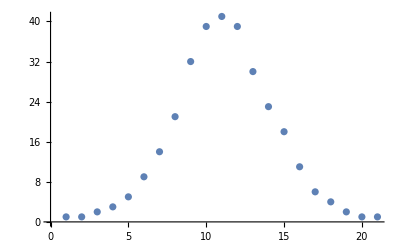

```mathematica
Map[#[[1,1,1]]&,res]//Tally//Sort//ListPlot
```

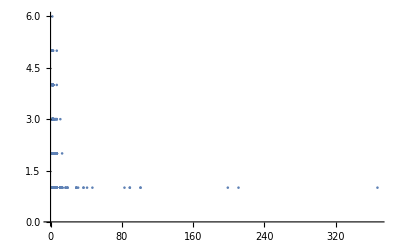

```mathematica
ListPlot[Flatten[Map[#[[1,2]]&,res]//FactorInteger,1],PlotRange->All]
```

```mathematica
2^21
```

2097152

```mathematica
n(n+1)/2/.n-> 7
```

28

```mathematica
2^28
```

268435456

```mathematica
With[
{size=8},
With[
{g=Graph[DeleteDuplicates[Recurse[Table[{i},{i,size}]]],VertexLabels->"Name"],
DoubleVertices=TwoElements[size],exp=2^(size*(size-1)/2)},
Block[{count=1},
TableForm[
Sort[
Tally[
Monitor[
Table[
count++;
PartitionIntersect[g,set],
{set, Subsets[DoubleVertices,{1,Length[DoubleVertices]}]}
],
{N[(count/exp)*100,20],Length[set]}]
]
],TableDepth->1
]
]
]
]
```

```mathematica
N[1/268435456,20]
```

3.7252902984619140625×10^-9